```mathematica
Manipulate[LogPlot[{n^m,3n-2},{n,10,10^6},PlotStyle->{Red,Green}],{m,1,3,.05}]
```

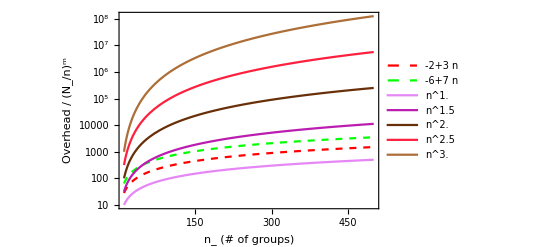

```mathematica
ms=Subdivide[1.,3.,4];
LogPlot[Evaluate[Join[{3n-2,7n-6},Table[n^m,{m,ms}]]],{n,10,5 10^2},PlotStyle->Join[{Directive[Red,Dashed],Directive[Green,Dashed]},RandomColor[7]],PlotLegends->"Expressions",FrameLabel->{"n_ (# of groups)","Overhead / (N_/n_)^m"},LabelStyle->Directive[Black,FontFamily->"Arial",13],FrameStyle->Directive[Black],FrameTicksStyle->Directive[Black]]
```

```mathematica
vals={(*𝒩->10^8,*)n->10^4,m->2.5+.5};
(*𝒩^m-(3n-2)(𝒩/n)^m/.vals*)
𝒩^m/((3n-2)(𝒩/n)^m)/.vals//ScientificForm
𝒩^m/((7n-6)(𝒩/n)^m)/.vals//ScientificForm
```

3.33356×10^7

1.42869×10^7

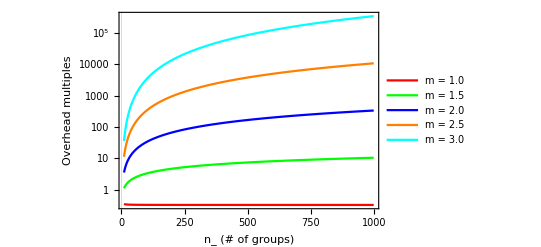

```mathematica
ms=Subdivide[1.,3.,4];
Plot[Evaluate[Table[n^m/(3n-2),{m,ms}]],{n,10,10^3},PlotStyle->(*RandomColor[5]*){Red,Green,Blue,Orange,Cyan},PlotLegends->StringTemplate["m_ = ``"]/@ms,FrameLabel->{"n_ (# of groups)","Overhead multiples"},LabelStyle->Directive[Black,FontFamily->"Arial",13],FrameStyle->Directive[Black],FrameTicksStyle->Directive[Black],ScalingFunctions->"Log"]
```

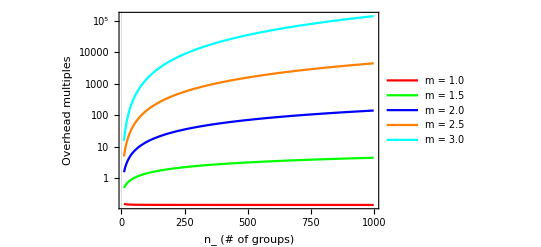

```mathematica
ms=Subdivide[1.,3.,4];
Plot[Evaluate[Table[n^m/(7n-6),{m,ms}]],{n,10,10^3},PlotStyle->(*RandomColor[5]*){Red,Green,Blue,Orange,Cyan},PlotLegends->StringTemplate["m_ = ``"]/@ms,FrameLabel->{"n_ (# of groups)","Overhead multiples"},LabelStyle->Directive[Black,FontFamily->"Arial",13],FrameStyle->Directive[Black],FrameTicksStyle->Directive[Black],ScalingFunctions->"Log"]
```

```mathematica
Quantity[1,"Billion""Years"]/Quantity[3,"Weeks"]//N
```

1.7381×10^10

```mathematica
n^m/(3n-2)/.{m->3.,n->100}//ScientificForm
n^m/(3n-2)/.{m->3.,n->10^8 10^-4}//ScientificForm
n^m/(3n-2)/.{m->2.5,n->100}//ScientificForm
n^m/(3n-2)/.{m->2.5,n->10^8 10^-4}//ScientificForm
```

3.3557×10^3

3.33356×10^7

3.3557×10^2

3.33356×10^5

```mathematica
100^2.5
100^3
```

100000.

1000000

```mathematica
TableForm[Table[ScientificForm[n^m/(3n-2)],{m,{2.,2.5,3.}},{n,{10^2,10^4}}],TableHeadings->{{"m = 2.0","2.5","3.0"},{"n = 10^2","10^4"}},TableAlignments->Right]
```

| n = 10^2 | 10^4
m = 2.0 | 3.3557×10^1 | 3.33356×10^3
2.5 | 3.3557×10^2 | 3.33356×10^5
3.0 | 3.3557×10^3 | 3.33356×10^7